```mathematica
(*Plot[{Sin[x],Cos[x]},{x,0,2π}]*)
```

```mathematica
(*s=NDSolve[{y'[x]==y[x]Cos[x+y[x]],y[0]==1},y,{x,0,30}];Plot[Evaluate[y[x]/.s],{x,0,30},PlotRange->All]*)
```

```mathematica
F浮=2
Print[F浮]
```

2

2

```mathematica
NDSolve[{D[u[t,x],t]==D[u[t,x],x,x],u[0,x]==0,u[t,0]==Sin[t],u[t,5]==0},u,{t,0,10},{x,0,5}];
Plot3D[Evaluate[u[t,x]/.%],{t,0,10},{x,0,5},PlotRange->All]
```

-Graphics3D-

## 问题 1

以下为问题 1(1) 参数。

```mathematica
m=2433;k=80000;c=10000;
f=6250;omega=1.4005;k1=1025*9.8*Pi;
c0=656.3616;m0=1335.535;M=4866;
```

110

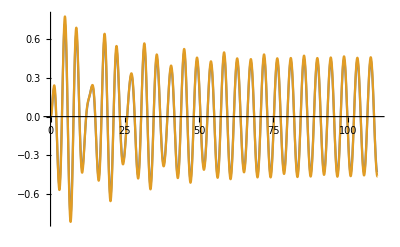

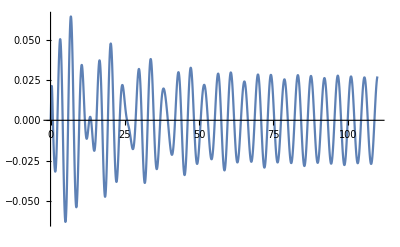

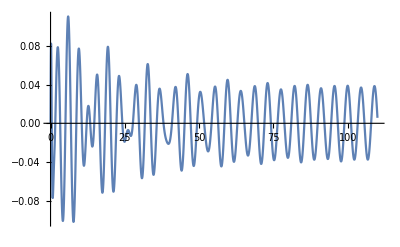

```mathematica
stop=110
s=NDSolve[{m*x2''[t]==k(x1[t]-x2[t])+c(x1'[t]-x2'[t]),f*Cos[omega*t]==k(x1[t]-x2[t])+c(x1'[t]-x2'[t])+k1*x1[t]+c0*x1'[t]+m0*x1''[t]+M*x1''[t],x1[0]==x2[0]==x1'[0]==x2'[0]==0},{x1,x2},{t,0,stop}];
Plot[Evaluate[{x1[t],x2[t]}/.s],{t,0,stop}]
Plot[Evaluate[x1[t]-x2[t]/.s],{t,0,stop}]
Plot[Evaluate[x1'[t]-x2'[t]/.s],{t,0,stop}]
```

求得对应位移和速度为：

```mathematica
targets={10,20,40,60,100};
Grid[Flatten[Table[{i,x1[i],x1'[i],x2[i],x2'[i]}/.s,{i,targets}],1],Frame->All]
```

10 | -0.190711 | -0.641009 | -0.211679 | -0.693954
20 | -0.590684 | -0.240952 | -0.634248 | -0.272776
40 | 0.285375 | 0.312972 | 0.2965 | 0.332913
60 | -0.314504 | -0.479455 | -0.331434 | -0.515728
100 | -0.0836139 | -0.604211 | -0.0840672 | -0.643001

修改为问题 1(2) 参数，重新计算。

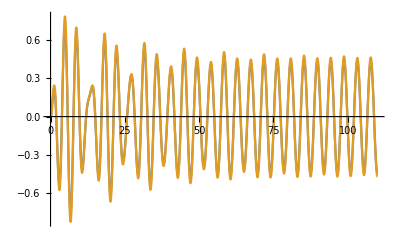

10 | -0.191991 | -0.644618 | -0.213781 | -0.701741
20 | -0.59419 | -0.245594 | -0.640176 | -0.28171
40 | 0.282215 | 0.306276 | 0.294026 | 0.325993
60 | -0.317233 | -0.482805 | -0.335615 | -0.520822
100 | -0.0848248 | -0.605817 | -0.0862466 | -0.645578

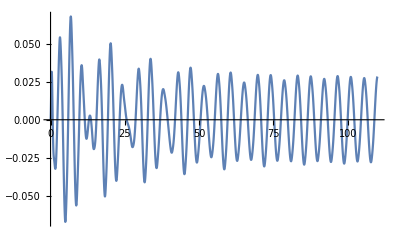

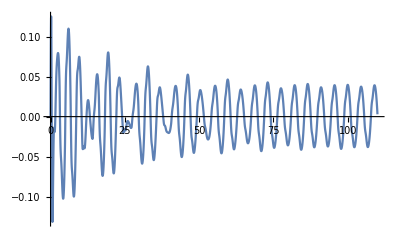

```mathematica
cv2[v_]:=10000*Sqrt[Abs[v]]
s=NDSolve[{m*x2''[t]==k(x1[t]-x2[t])+cv2[x2'[t]]*(x1'[t]-x2'[t]),f*Cos[omega*t]==k(x1[t]-x2[t])+cv2[x2'[t]]*(x1'[t]-x2'[t])+k1*x1[t]+c0*x1'[t]+m0*x1''[t]+M*x1''[t],x1[0]==x2[0]==x1'[0]==x2'[0]==0},{x1,x2},{t,0,stop}];
Plot[Evaluate[{x1[t],x2[t]}/.s],{t,0,stop}]
Grid[Flatten[Table[{i,x1[i],x1'[i],x2[i],x2'[i]}/.s,{i,targets}],1],Frame->All]
Plot[Evaluate[x1[t]-x2[t]/.s],{t,0,stop}]
Plot[Evaluate[x1'[t]-x2'[t]/.s],{t,0,stop}]
```

## 问题 2

以下为问题 2(1) 参数。

```mathematica
(*NMaximize[x1[t]/.s,t]*)
```

```mathematica
M=4866;m=2433;k=80000;c=10000;omega=2.2143;k1=1025*9.8*Pi;
f=4890;c0=167.8395;m0=1165.992;
```

```mathematica
start=510;stop=520;dim=1;
P2[cm2_]:=Sum[cm2*((x1'[i]-x2'[i])^2)*dim,{i,start,stop,dim}]/.NDSolve[{m*x2''[t]==k*(x1[t]-x2[t])+cm2*(x1'[t]-x2'[t]),f*Cos[omega*t]==k*(x1[t]-x2[t])+cm2*(x1'[t]-x2'[t])+k1*x1[t]+c0*x1'[t]+m0*x1''[t]+M*x1''[t],x1[0]==x2[0]==x1'[0]==x2'[0]==0},{x1,x2},{t,start,stop}]
```

```mathematica
(*NMaximize[P2[cm2],cm2]*)
```

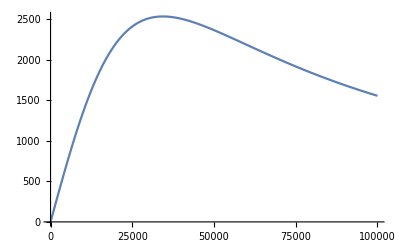

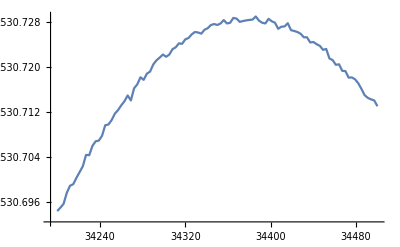

```mathematica
DrawP2[pStart_,pStop_,pStepNum_]:=ListLinePlot[Table[{i,First[P2[i]]},{i,Range[pStart,pStop,(pStop-pStart)/pStepNum]}]]
DrawP2[0,100000,100]
DrawP2[34200,34500,100]
```

```mathematica
M=4866;m=2433;k=80000;c=10000;omega=2.2143;k1=1025*9.8*Pi;
f=4890;c0=167.8395;m0=1165.992;
cmv2[v_,ck_,ce_]:=ck*Abs[v]^ce;
P22I[ck_,ce_]:=NDSolve[{m*x2''[t]==k*(x1[t]-x2[t])+cmv2[x1'[t]-x2'[t],ck,ce]*(x1'[t]-x2'[t]),f*Cos[omega*t]==k*(x1[t]-x2[t])+cmv2[x1'[t]-x2'[t],ck,ce]*(x1'[t]-x2'[t])+k1*x1[t]+c0*x1'[t]+m0*x1''[t]+M*x1''[t],x1[0]==x2[0]==x1'[0]==x2'[0]==0},{x1,x2},{t,start,stop}]
P22[ck_,ce_]:=Sum[cmv2[x1'[i]-x2'[i],ck,ce+2]*dim,{i,start,stop,dim}]/.P22I[ck,ce]
CalcP22[kStart_,kStop_,kStepNum_,eStart_,eStop_,eStepNum_]:=Table[{pe,ppk,First[P22[ppk,pe]]},{ppk,Range[kStart,kStop,(kStop-kStart)/kStepNum]},{pe,Range[eStart,eStop,(eStop-eStart)/eStepNum]}]
DrawP22[data_]:=ListPlot3D[Flatten[data,1]]
(*DrawP22[0,10000,10,0,1,10]*)
CalcP22[0,100000,10,0,1,10];
(*DrawP22[34200,34500,100]*)
(*First[P22[2,2]]*)
```

```mathematica
s=%;
```

```mathematica
(*s_x=Table[{i[[0]]},{i,s}]s_y=Table[{i[[1]]},{i,s}]s2=Table[]*)
```

{0.,0.,0.} | {0.1,0.,0.} | {0.2,0.,0.} | {0.3,0.,0.} | {0.4,0.,0.} | {0.5,0.,0.} | {0.6,0.,0.} | {0.7,0.,0.} | {0.8,0.,0.} | {0.9,0.,0.} | {1.,0.,0.}
{0.,10000.,1356.19} | {0.1,10000.,1127.19} | {0.2,10000.,929.929} | {0.3,10000.,763.314} | {0.4,10000.,624.417} | {0.5,10000.,509.663} | {0.6,10000.,415.454} | {0.7,10000.,338.463} | {0.8,10000.,275.761} | {0.9,10000.,224.835} | {1.,10000.,183.567}
{0.,20000.,2198.8} | {0.1,20000.,1941.41} | {0.2,20000.,1673.52} | {0.3,20000.,1417.42} | {0.4,20000.,1185.54} | {0.5,20000.,982.796} | {0.6,20000.,809.618} | {0.7,20000.,664.049} | {0.8,20000.,543.049} | {0.9,20000.,443.266} | {1.,20000.,361.456}
{0.,30000.,2507.3} | {0.1,30000.,2374.45} | {0.2,30000.,2160.09} | {0.3,30000.,1906.75} | {0.4,30000.,1645.44} | {0.5,30000.,1395.37} | {0.6,30000.,1168.43} | {0.7,30000.,969.563} | {0.8,30000.,799.347} | {0.9,30000.,656.021} | {1.,30000.,536.732}
{0.,40000.,2501.81} | {0.1,40000.,2524.95} | {0.2,40000.,2422.47} | {0.3,40000.,2231.79} | {0.4,40000.,1991.59} | {0.5,40000.,1734.66} | {0.6,40000.,1482.14} | {0.7,40000.,1247.99} | {0.8,40000.,1039.82} | {0.9,40000.,859.819} | {1.,40000.,707.134}
{0.,50000.,2362.03} | {0.1,50000.,2513.26} | {0.2,50000.,2525.69} | {0.3,50000.,2422.62} | {0.4,50000.,2235.74} | {0.5,50000.,1999.68} | {0.6,50000.,1746.03} | {0.7,50000.,1495.3} | {0.8,50000.,1261.36} | {0.9,50000.,1052.4} | {1.,50000.,871.109}
{0.,60000.,2181.51} | {0.1,60000.,2422.96} | {0.2,60000.,2531.47} | {0.3,60000.,2514.85} | {0.4,60000.,2394.79} | {0.5,60000.,2199.5} | {0.6,60000.,1961.39} | {0.7,60000.,1709.39} | {0.8,60000.,1462.01} | {0.9,60000.,1232.22} | {1.,60000.,1027.5}
{0.,70000.,2000.33} | {0.1,70000.,2300.26} | {0.2,70000.,2482.84} | {0.3,70000.,2541.51} | {0.4,70000.,2487.78} | {0.5,70000.,2343.11} | {0.6,70000.,2133.73} | {0.7,70000.,1891.22} | {0.8,70000.,1640.7} | {0.9,70000.,1398.23} | {1.,70000.,1175.45}
{0.,80000.,1833.27} | {0.1,80000.,2168.54} | {0.2,80000.,2406.26} | {0.3,80000.,2526.7} | {0.4,80000.,2533.32} | {0.5,80000.,2439.95} | {0.6,80000.,2268.13} | {0.7,80000.,2043.96} | {0.8,80000.,1797.63} | {0.9,80000.,1549.81} | {1.,80000.,1314.38}
{0.,90000.,1684.32} | {0.1,90000.,2039.4} | {0.2,90000.,2316.08} | {0.3,90000.,2486.93} | {0.4,90000.,2545.68} | {0.5,90000.,2500.97} | {0.6,90000.,2368.81} | {0.7,90000.,2170.58} | {0.8,90000.,1934.54} | {0.9,90000.,1686.76} | {1.,90000.,1443.86}
{0.,100000.,1553.23} | {0.1,100000.,1917.92} | {0.2,100000.,2221.3} | {0.3,100000.,2432.57} | {0.4,100000.,2535.54} | {0.5,100000.,2534.93} | {0.6,100000.,2441.68} | {0.7,100000.,2273.5} | {0.8,100000.,2053.18} | {0.9,100000.,1809.75} | {1.,100000.,1563.7}

-Graphics3D-

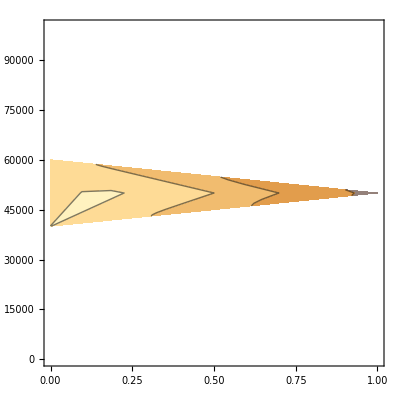

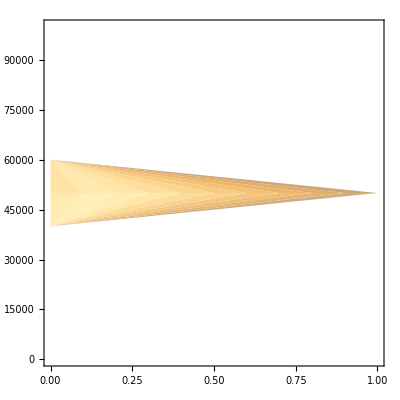

```mathematica
Grid[N[s]]
ListPlot3D[Flatten[s,1]]
ListContourPlot[Flatten[s,1]]
ListDensityPlot[Flatten[s,1]]
```

```mathematica
Max[Table[i[[3]],{i,Flatten[s,1]}]]
```

2545.68

{{{0,0,0},{0,1,1},{0,2,4},{0,3,9},{0,4,16},{0,5,25},{0,6,36},{0,7,49},{0,8,64},{0,9,81},{0,10,100}},{{1,0,1},{1,1,2},{1,2,5},{1,3,10},{1,4,17},{1,5,26},{1,6,37},{1,7,50},{1,8,65},{1,9,82},{1,10,101}},{{2,0,4},{2,1,5},{2,2,8},{2,3,13},{2,4,20},{2,5,29},{2,6,40},{2,7,53},{2,8,68},{2,9,85},{2,10,104}},{{3,0,9},{3,1,10},{3,2,13},{3,3,18},{3,4,25},{3,5,34},{3,6,45},{3,7,58},{3,8,73},{3,9,90},{3,10,109}},{{4,0,16},{4,1,17},{4,2,20},{4,3,25},{4,4,32},{4,5,41},{4,6,52},{4,7,65},{4,8,80},{4,9,97},{4,10,116}},{{5,0,25},{5,1,26},{5,2,29},{5,3,34},{5,4,41},{5,5,50},{5,6,61},{5,7,74},{5,8,89},{5,9,106},{5,10,125}},{{6,0,36},{6,1,37},{6,2,40},{6,3,45},{6,4,52},{6,5,61},{6,6,72},{6,7,85},{6,8,100},{6,9,117},{6,10,136}},{{7,0,49},{7,1,50},{7,2,53},{7,3,58},{7,4,65},{7,5,74},{7,6,85},{7,7,98},{7,8,113},{7,9,130},{7,10,149}},{{8,0,64},{8,1,65},{8,2,68},{8,3,73},{8,4,80},{8,5,89},{8,6,100},{8,7,113},{8,8,128},{8,9,145},{8,10,164}},{{9,0,81},{9,1,82},{9,2,85},{9,3,90},{9,4,97},{9,5,106},{9,6,117},{9,7,130},{9,8,145},{9,9,162},{9,10,181}},{{10,0,100},{10,1,101},{10,2,104},{10,3,109},{10,4,116},{10,5,125},{10,6,136},{10,7,149},{10,8,164},{10,9,181},{10,10,200}}}

{0.,0.,0.} | {0.,1.,1.} | {0.,2.,4.} | {0.,3.,9.} | {0.,4.,16.} | {0.,5.,25.} | {0.,6.,36.} | {0.,7.,49.} | {0.,8.,64.} | {0.,9.,81.} | {0.,10.,100.}
{1.,0.,1.} | {1.,1.,2.} | {1.,2.,5.} | {1.,3.,10.} | {1.,4.,17.} | {1.,5.,26.} | {1.,6.,37.} | {1.,7.,50.} | {1.,8.,65.} | {1.,9.,82.} | {1.,10.,101.}
{2.,0.,4.} | {2.,1.,5.} | {2.,2.,8.} | {2.,3.,13.} | {2.,4.,20.} | {2.,5.,29.} | {2.,6.,40.} | {2.,7.,53.} | {2.,8.,68.} | {2.,9.,85.} | {2.,10.,104.}
{3.,0.,9.} | {3.,1.,10.} | {3.,2.,13.} | {3.,3.,18.} | {3.,4.,25.} | {3.,5.,34.} | {3.,6.,45.} | {3.,7.,58.} | {3.,8.,73.} | {3.,9.,90.} | {3.,10.,109.}
{4.,0.,16.} | {4.,1.,17.} | {4.,2.,20.} | {4.,3.,25.} | {4.,4.,32.} | {4.,5.,41.} | {4.,6.,52.} | {4.,7.,65.} | {4.,8.,80.} | {4.,9.,97.} | {4.,10.,116.}
{5.,0.,25.} | {5.,1.,26.} | {5.,2.,29.} | {5.,3.,34.} | {5.,4.,41.} | {5.,5.,50.} | {5.,6.,61.} | {5.,7.,74.} | {5.,8.,89.} | {5.,9.,106.} | {5.,10.,125.}
{6.,0.,36.} | {6.,1.,37.} | {6.,2.,40.} | {6.,3.,45.} | {6.,4.,52.} | {6.,5.,61.} | {6.,6.,72.} | {6.,7.,85.} | {6.,8.,100.} | {6.,9.,117.} | {6.,10.,136.}
{7.,0.,49.} | {7.,1.,50.} | {7.,2.,53.} | {7.,3.,58.} | {7.,4.,65.} | {7.,5.,74.} | {7.,6.,85.} | {7.,7.,98.} | {7.,8.,113.} | {7.,9.,130.} | {7.,10.,149.}
{8.,0.,64.} | {8.,1.,65.} | {8.,2.,68.} | {8.,3.,73.} | {8.,4.,80.} | {8.,5.,89.} | {8.,6.,100.} | {8.,7.,113.} | {8.,8.,128.} | {8.,9.,145.} | {8.,10.,164.}
{9.,0.,81.} | {9.,1.,82.} | {9.,2.,85.} | {9.,3.,90.} | {9.,4.,97.} | {9.,5.,106.} | {9.,6.,117.} | {9.,7.,130.} | {9.,8.,145.} | {9.,9.,162.} | {9.,10.,181.}
{10.,0.,100.} | {10.,1.,101.} | {10.,2.,104.} | {10.,3.,109.} | {10.,4.,116.} | {10.,5.,125.} | {10.,6.,136.} | {10.,7.,149.} | {10.,8.,164.} | {10.,9.,181.} | {10.,10.,200.}

-Graphics3D-

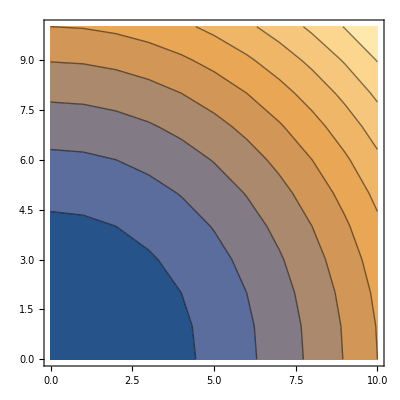

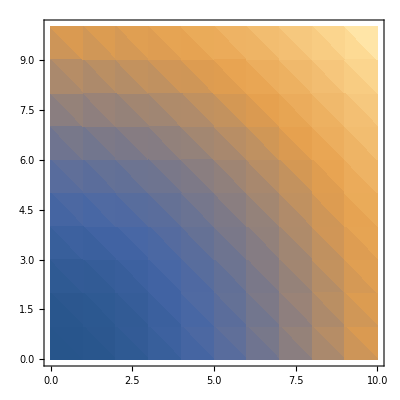

```mathematica
ttt=Table[{i,j,i^2+j^2},{i,Range[0,10]},{j,Range[0,10]}]
Grid[N[ttt]]
ListPlot3D[Flatten[ttt,1]]
ListContourPlot[Flatten[ttt,1]]
ListDensityPlot[Flatten[ttt,1]]
```

```mathematica
(*fun=Abs[f*Cos[omega*t]*0.5*2/1.4]Integrate[fun,{t,1000,1100}]*)
```

4464.29 Abs[Cos[1.4005 t]]

285377.

## 问题 3

```mathematica
Clear["Global`*"];
(*AG长度*)
d=1.40792;
(*弹簧原长度*)
l0=0.5;
(*振子质量*)
m=1;
(*弹簧劲度系数*)
k=8000;
(*直线阻尼器阻尼系数*)
c=10000;
(*小g*)
g=9.8;
(*弹簧旋转刚度*)
krot=250000;
(*旋转阻尼器阻尼系数*)
krot=1000;
(*浮子质量*)
M=4866;
(*垂荡兴波阻尼系数*)
c0=683.4558;
(*纵摇附加转动惯量*)
I0=7001.914;
(*纵摇激励力矩振幅*)
L=1690;
(*入射波浪频率*)
w=1.7152;
(*垂荡激励力振幅*)
f=3640;
(*浮子转动惯量*)
Ia=4866/(7π+(Sqrt[41]π)/5)*(Integrate[1/0.8*2*Pi*(r+(17.6+8/75*(Sqrt[41]))/(7+(Sqrt[41])/5))*r^2,{r,-(17.6+8/75*(Sqrt[41]))/(7+(Sqrt[41])/5),-(17.6+8/75*(Sqrt[41]))/(7+(Sqrt[41])/5)+0.8}]+Integrate[2*Pi*r^2,{r,-(17.6+8/75*(Sqrt[41]))/(7+(Sqrt[41])/5)+0.8,-(17.6+8/75*(Sqrt[41]))/(7+(Sqrt[41])/5)+3.8}]+Integrate[2*Pi*(3.8-(17.6+8/75*(Sqrt[41]))/(7+(Sqrt[41])/5))^2+a^2,{a,0,0.5}]);
(*垂荡附加质量*)
m0=1028.876;
(*纵摇兴波阻尼力矩系数*)
crot:=654.3383;
(*纵摇静水恢复力矩系数*)
Mrec:=8890.7;

(*垂荡静水恢复力(浮力)*)
Fj[t_]:=7.120975609756098-Pi*zg[t]
(*激励力*)
Fwave[t_]:=f*Cos[w*t];
(*振子转动惯量*)
Ib[t_]=258.149+774.448l[t]+1548.9l[t]^2;
(*x方向F*)
Fx[t_]:=1*Abs[zg'[t]];
(*纵摇激励力矩*)
Mwave[t_]:=L*Cos[w*t];
(*A点z座标*)
(*za[t_]:=zg[t]-d*Cos[th[t]];*)
(*theta2=theta1+gamma*)
th2[t_]:=th[t]+ga[t];
(*P点x座标*)
xp[t_]:=d*Sin[th[t]]-l[t]*Sin[th2[t]];
(*P点z座标*)
zp[t_]:=zg[t]-d*Cos[th[t]]+l[t]*Cos[th2[t]];
(*PTO系统的力*)
Fpto[t_]:=-k*(l[t]-l0)-c*l'[t];
(*PTO系统的力矩*)
Mpto[t_]:=-krot*ga[t]-crot*ga'[t];
(*轻杆对振子支持力x分力*)
Fabx[t_]:=Fpto[t]*Sin[th2[t]]
(*轻杆对振子支持力z分力*)
Fabz[t_]:=m*zp''[t]+m*g-Fpto[t]*Cos[th2[t]]
NDSolve[{m*xp''[t]==-Fpto[t]*Sin[th2[t]]+Fabx[t],Ib[t]*th2''[t]==Mpto[t]+Fabx[t]*l[t]*Cos[th2[t]]-Fabz[t]*l[t]*Sin[th2[t]],(*Fwave[t]-M*g-Fpto[t]*Cos[th2[t]]-Fx-Ff==M*zg''[t],*)M*zg''[t]==Fwave[t]+Fj[t]-M*g-Fpto[t]*Cos[th2[t]]-Fabz[t]-m0*zg''[t]-c0*zg'[t]Ia*th''[t]==Mwave[t]-Mpto[t]+Fabx[t]*d*Cos[th[t]]-Fabz[t]*d*Sin[th[t]]-I0*th''[t]-crot*th'[t]-Mrec*th[t],th[0]==th'[0]==ga[0]==ga'[0]==l'[0]==zg'[0]==0},{th,ga,zg,l},{t,0,100},Method->{"EquationSimplification"->"Residual"}]
```

$Aborted